```mathematica
J[{a_,b_}]:={-b,a}
```

```mathematica
(D[{x[t],y[t]},{t,2}].J[D[{x[t],y[t]},t]])/(‖D[{x[t],y[t]},t]‖)^3
```

(-y'[t] x''[t]+x'[t] y''[t])/(‖{x'[t],y'[t]}‖)^3

```mathematica
DoubleBracketingBar[x]
```

‖x‖

```mathematica
With[{x=Identity},
(-y'[t] x''[t]+x'[t] y''[t])/(‖{x'[t],y'[t]}‖)^3]
```

y''[t]/(‖{1,y'[t]}‖)^3

```mathematica
With[{x=Identity,y=Identity},
(-y'[t] x''[t]+x'[t] y''[t])/(‖{x'[t],y'[t]}‖)^3]
```

0

```mathematica
With[{x=Identity,y=Function[x,√(1-x^2)]},
(-y'[t] x''[t]+x'[t] y''[t])/(‖{x'[t],y'[t]}‖)^3]
```

(-t^2/((1-t^2)^(3/2))-1/(√(1-t^2)))/((‖{1,-t/(√(1-t^2))}‖)^3)

```mathematica
y''[t]/(‖{1,y'[t]}‖)^3
```

y''[t]/(‖{1,y'[t]}‖)^3

```mathematica
y''[t]/(‖{1,y'[t]}‖)^3==y[t]
```

y''[t]/(‖{1,y'[t]}‖)^3==y[t]

```mathematica
y''[t]/(‖{1,y'[t]}‖)^3==0
```

y''[t]/(‖{1,y'[t]}‖)^3==0

```mathematica
DSolve[y''[t]/(‖{1,y'[t]}‖)^3==0,y[t],t]
```

{{y[t]→C[1]+t C[2]}}

```mathematica
DSolve[y''[t]/(‖{1,y'[t]}‖)^3==1,y[t],t]
```

{{y[t]→C[2]+InverseFunction[1/(‖{1,K[1]}‖)^3K[1]1#1&][C[1]+K[2]]K[2]1t}}

```mathematica
Norm[{1,y'[t]}]^3
```

(1+Abs[y'[t]]^2)^(3/2)

```mathematica
FullSimplify[Norm[{1,y'[t]}]^3,{t,y[t],y'[t]}∈Reals]
```

(1+y'[t]^2)^(3/2)

```mathematica
(1+y'[t]^2)^(3/2)
```

```mathematica
DSolve[y''[t]/((1+y'[t]^2)^(3/2))==1,y[t],t]
```

{{y[t]→-ⅈ √(-1+t^2+2 t C[1]+C[1]^2)+C[2]},{y[t]→ⅈ √(-1+t^2+2 t C[1]+C[1]^2)+C[2]}}

```mathematica
ComplexPlot[-ⅈ √(-1+t^2+4t +2^2)+1,{t,-2,2}]
```

ComplexPlot::plld: Corners for t in {t,-2,2} must have distinct machine-precision real and imaginary parts.

ComplexPlot[-ⅈ √(-1+t^2+4 t+2^2)+1,{t,-2,2}]

```mathematica
ⅈ x
```

ⅈ x

```mathematica
ComplexPlot[-ⅈ √(-1+t^2+4 t+2^2)+1,{t,-2-2ⅈ,2+2ⅈ}]
```

-Graphics-

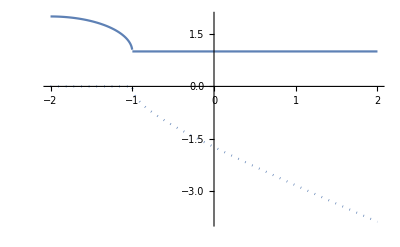

```mathematica
ReImPlot[-ⅈ √(-1+t^2+4 t+2^2)+1,{t,-2,2}]
```

```mathematica
LaplaceTransform[√(1-t^2),t,s]
```

(π BesselI[1,s]+2 ⅈ BesselK[1,s]-π StruveL[1,s])/(2 s)

```mathematica
ComplexPlot[(π BesselI[1,s]+2 ⅈ BesselK[1,s]-π StruveL[1,s])/(2 s),{s,-2-2I,2+2I}]
```

-Graphics-

```mathematica
2+2==4
```

True

```mathematica
Reals
```

ℝ

```mathematica
Reals+Reals==Reals
```

2 ℝ==ℝ

```mathematica
f:Reals->Reals
```

f:ℝ→ℝ

```mathematica
Equal@@(f:Reals->Reals)
```

(f:ℝ)==ℝ

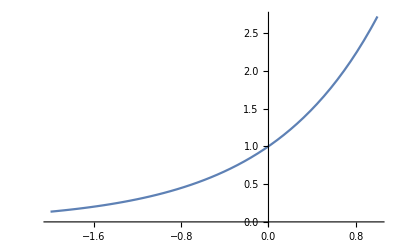

```mathematica
Plot[Exp[x],{x,-2,1}]
```

```mathematica
Exp''[x]/(Norm[)
```

```mathematica
With[{y=Exp},
y''[t]/(‖{1,y'[t]}‖)^3]
```

ⅇ^t/((‖{1,ⅇ^t}‖)^3)

```mathematica
With[{y=Exp},
y''[t]/Norm[{1,y'[t]}]^3]
```

ⅇ^t/((1+ⅇ^(2 Re[t]))^(3/2))

```mathematica
With[{y=Exp},
FullSimplify[y''[t]/Norm[{1,y'[t]}]^3,Element[t,Reals]]
]
```

ⅇ^t/((1+ⅇ^(2 t))^(3/2))

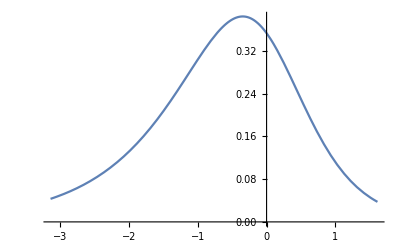

```mathematica
Plot[ⅇ^t/((1+ⅇ^(2 t))^(3/2)),{t,-3.13959465092712,1.6114359150967734}]
```

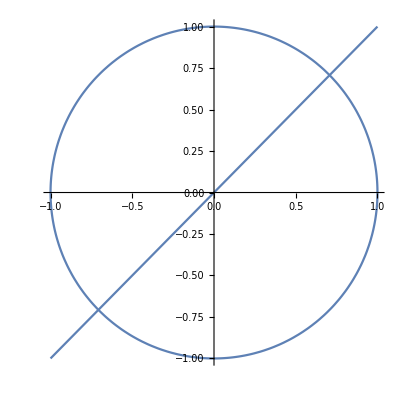

```mathematica
Show[{
ParametricPlot[{Cos[t],Sin[t]},{t,0,2π}],
Plot[x,{x,-1,1}]
}]
```

```mathematica
Show[{
ParametricPlot[{Cos[t],Sin[t]},{t,0,2π}],
Plot[x,{x,-1,1}]
}]
```

```mathematica
Manipulate[
Show[{
ParametricPlot[{a+Cos[t],a+Sin[t]},{t,0,2π}],
Plot[x,{x,-2,2}]
}],{a,-1,1}]
```

```mathematica
Manipulate[
Show[{
ParametricPlot[{a+Cos[t],a+Sin[t]},{t,0,2π}],
Plot[x^3,{x,-2,2}]
}],{a,-1,1}]
```

```mathematica
With[{f=Function[x,x^3]},
f
]
```

Function[x,x^3]

```mathematica
With[{y=Function[x,x^3]},
With[{curve=y''[t]/Norm[{1,y'[t]}]^3},
curve
]]
```

(6 t)/((1+9 Abs[t]^4)^(3/2))

```mathematica
With[{y=Function[x,x^3]},
With[{curve=FullSimplify[y''[t]/Norm[{1,y'[t]}]^3,Element[t,Reals]]},
curve
]]
```

(6 t)/((1+9 t^4)^(3/2))

```mathematica
With[{y=Function[x,x^3]},
With[{curve=FullSimplify[y''[t]/Norm[{1,y'[t]}]^3,Element[t,Reals]]},
Manipulate[curve,{a,-2,2}]
]]
```

```mathematica
With[{y=Function[x,x^3]},
With[{curve=Function[t,FullSimplify[y''[t]/Norm[{1,y'[t]}]^3,Element[t,Reals]]]},
Manipulate[
Show[{
ParametricPlot[{a+Cos[t]/curve[a],a+Sin[t]/curve[a]},{t,0,2π}],
Plot[x^3,{x,-2,2}]
}]
,{a,-2,2}]
]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
With[{y=Function[x,x^3]},
With[{curve=Function[t,FullSimplify[y''[t]/Norm[{1,y'[t]}]^3,Element[t,Reals]]]},
Manipulate[
Show[{
ParametricPlot[{a+Cos[t]/curve[a],a+Sin[t]/curve[a]},{t,0,2π},PlotRange->{-1,1}],
Plot[x^3,{x,-2,2},PlotRange->{-1,1}]
}]
,{a,-2,2}]
]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
Exp[f'[x]/f[x]]
```

ⅇ^(f'[x]/f[x])

```mathematica
Exp[f'[x]/f[x]]==f[x]
```

ⅇ^(f'[x]/f[x])==f[x]

```mathematica
DSolve[ⅇ^(f'[x]/f[x])==f[x],{f[x]},{x}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f[x]→ⅇ^(ⅇ^(x+C[1]))}}

```mathematica
Exp[f'[x]/f[x]]==x
```

ⅇ^(f'[x]/f[x])==x

```mathematica
DSolve[ⅇ^(f'[x]/f[x])==x,{f[x]},{x}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f[x]→ⅇ^(-x+x Log[x]) C[1]}}

```mathematica
ⅇ^(-x+x Log[x])
```

ⅇ^(-x+x Log[x])

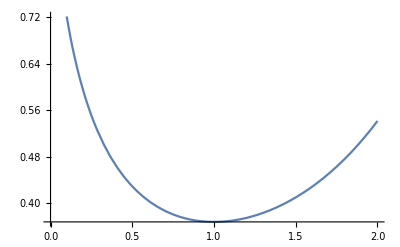

```mathematica
Plot[ⅇ^(-x+x Log[x]),{x,0,2}]
```

```mathematica
With[{y=Function[x,ⅇ^(-x+x Log[x])]},
With[{curve=Function[t,FullSimplify[y''[t]/Norm[{1,y'[t]}]^3,Element[t,Reals]]]},
Manipulate[
Show[{
ParametricPlot[{a+Cos[t]/curve[a],a+Sin[t]/curve[a]},{t,0,2π},PlotRange->{-5,5}],
Plot[y[x],{x,0,4},PlotRange->{-5,5}]
}]
,{a,0,4}]
]]
```

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
FullSimplify[
Normalize[{0,f''[x]}].Normalize[{-f'[x],1}]
,{x,f[x],f'[x],f''[x]}∈Reals]
```

Sign[f''[x]]/(√(1+f'[x]^2))

```mathematica
With[{f=Identity},
FullSimplify[
Normalize[{0,f''[x]}].Normalize[{-f'[x],1}]
,{x,f[x],f'[x],f''[x]}∈Reals]
]
```

0

```mathematica
With[{f=Function[x,x^2]},
FullSimplify[
Normalize[{0,f''[x]}].Normalize[{-f'[x],1}]
,{x,f[x],f'[x],f''[x]}∈Reals]
]
```

1/(√(1+4 x^2))

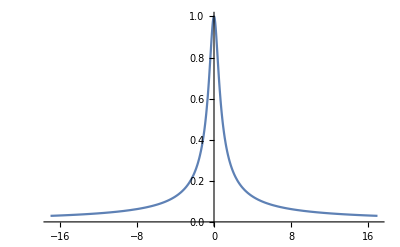

```mathematica
Plot[1/(√(1+4 x^2)),{x,-16.986666666666668,16.986666666666668},PlotRange->{0,1}]
```

```mathematica
With[{f=Function[x,x^2]},
FullSimplify[
Normalize[{0,f''[x]}].Normalize[{1,f'[x]}]
,{x,f[x],f'[x],f''[x]}∈Reals]
]
```

(2 x)/(√(1+4 x^2))

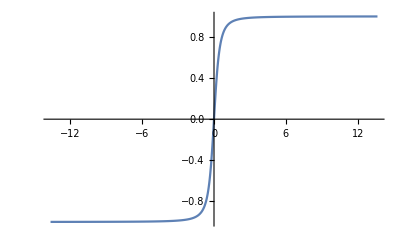

```mathematica
Plot[(2 x)/(√(1+4 x^2)),{x,-13.649999999999999,13.649999999999999}]
```

```mathematica
Integrate[(2 x)/(√(1+4 x^2)),x]
```

1/2 √(1+4 x^2)

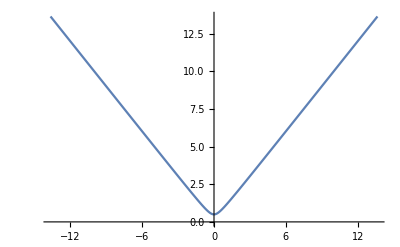

```mathematica
Plot[1/2 √(1+4 x^2),{x,-13.649999999999999,13.649999999999999}]
```

```mathematica
√(1+f''[x]^2)
```

√(1+f''[x]^2)

```mathematica
With[{f=Function[x,x^2/2]},
∫_0^1 √(1+f''[x]^2)ⅆx
]
```

√2

```mathematica
(1-a)p+a q
```

(1-a) p+a q

```mathematica
FullSimplify[
Normalize[{x,(1-a)p[x]+a q[x]}].Normalize[{x,p[x]}],{x,p[x],q[x]}∈Reals]
```

(x^2+p[x] (p[x]-a p[x]+a q[x]))/(√((x^2+Abs[p[x]-a p[x]+a q[x]]^2) (x^2+p[x]^2)))

```mathematica
FullSimplify[
Normalize[{x,(1-a)p[x]+a q[x]}].Normalize[{x,p[x]}],{x,a,p[x],q[x]}∈Reals]
```

(x^2+p[x] (p[x]-a p[x]+a q[x]))/(√((x^2+p[x]^2) (x^2+(p[x]-a p[x]+a q[x])^2)))

```mathematica
(x^2+p[x] (p[x]-a p[x]+a q[x]))/(√((x^2+p[x]^2) (x^2+(p[x]-a p[x]+a q[x])^2)))==a
```

(x^2+p[x] (p[x]-a p[x]+a q[x]))/(√((x^2+p[x]^2) (x^2+(p[x]-a p[x]+a q[x])^2)))==a

```mathematica
Reduce[(x^2+p[x] (p[x]-a p[x]+a q[x]))/(√((x^2+p[x]^2) (x^2+(p[x]-a p[x]+a q[x])^2)))==a]
```

Reduce[(x^2+p[x] (p[x]-a p[x]+a q[x]))/(√((x^2+p[x]^2) (x^2+(p[x]-a p[x]+a q[x])^2)))==a]

```mathematica
With[{p=Identity},
(x^2+p[x] (p[x]-a p[x]+a q[x]))/(√((x^2+p[x]^2) (x^2+(p[x]-a p[x]+a q[x])^2)))]
```

(x^2+x (x-a x+a q[x]))/(√2 √(x^2 (x^2+(x-a x+a q[x])^2)))

```mathematica
With[{p=Identity,q=Exp},
(x^2+p[x] (p[x]-a p[x]+a q[x]))/(√((x^2+p[x]^2) (x^2+(p[x]-a p[x]+a q[x])^2)))]
```

(x^2+x (a ⅇ^x+x-a x))/(√2 √(x^2 (x^2+(a ⅇ^x+x-a x)^2)))

```mathematica
FullSimplify[(x^2+x (a ⅇ^x+x-a x))/(√2 √(x^2 (x^2+(a ⅇ^x+x-a x)^2)))]
```

(x (a (ⅇ^x-x)+2 x))/(√2 √(x^2 (x^2+(a (ⅇ^x-x)+x)^2)))

```mathematica
Manipulate[Plot[(x (a (ⅇ^x-x)+2 x))/(√2 √(x^2 (x^2+(a (ⅇ^x-x)+x)^2))),{x,-3.911678202600524,1.0926896308681748}],{a,0,1}]
```

```mathematica
Manipulate[
Plot[(x (a (ⅇ^x-x)+2 x))/(√2 √(x^2 (x^2+(a (ⅇ^x-x)+x)^2))),
{x,-4,4},
PlotRange->{-1,1}],
{a,0,1}]
```

```mathematica
FullSimplify[
Normalize[{x,(1-a)p[x]+a q[x]}].Normalize[{x,q[x]}],{x,a,p[x],q[x]}∈Reals]
```

(x^2+q[x] (p[x]-a p[x]+a q[x]))/(√((x^2+q[x]^2) (x^2+(p[x]-a p[x]+a q[x])^2)))

```mathematica
With[{p=Identity,q=Exp},
(x^2+q[x] (p[x]-a p[x]+a q[x]))/(√((x^2+q[x]^2) (x^2+(p[x]-a p[x]+a q[x])^2)))]
```

(x^2+ⅇ^x (a ⅇ^x+x-a x))/(√((ⅇ^(2 x)+x^2) (x^2+(a ⅇ^x+x-a x)^2)))

```mathematica
Manipulate[Plot[(x^2+ⅇ^x (a ⅇ^x+x-a x))/(√((ⅇ^(2 x)+x^2) (x^2+(a ⅇ^x+x-a x)^2))),{x,-1.5382116608209202,1.5382116608209202}],{a,0,1}]
```